```mathematica
SetDirectory[NotebookDirectory[]];
```

# Self consistent Ascasibar et al. model

## Swept of different initial metallicity values for the Ascasibar et al. model with constant τS and directly coupled number densities.

## Constants

```mathematica
τS=26/10;(*[Gyr]*)
R=18/100;
ηion=95529/100;
ηdiss=38093/100;
C1=303/100000000; (*[Gyr]*)
C2=874/10000000; (*[Gyr]*)
Zsun=134/10000;
Zsn=9/100;
Zeff=Zsun*10^-3;
```

## Auxiliary function

```mathematica
g=i[t]+a[t]+m[t];
ψ=m[t]/τS;
Z=z[t]/g;
τR=C1/i[t];
τC=C2/(a[t]+m[t])*1/(Z+Zeff);
```

## ODE system

### Initial conditions and parameters for test run and time measurement

```mathematica
g0=10000;(*[M_(\[PermutationProduct]) pc^-3]*)
i0=g0*1/1000;(*[M_(\[PermutationProduct]) pc^-3]*)
a0=g0*500/1000;(*[M_(\[PermutationProduct]) pc^-3]*)
m0=g0*499/1000;(*[M_(\[PermutationProduct]) pc^-3]*)
s0=g0*0;(*[M_(\[PermutationProduct]) pc^-3]*)
z0=g0*zf0;(*[M_(\[PermutationProduct]) pc^-3]*)
Ini={i0,a0,m0,s0,z0};
```

```mathematica
Tstart=0; (*[Gyr]*)
Tend=1; (*[Gyr]*)
```

### System

```mathematica
var={i[t],a[t],m[t],s[t],z[t]};
equ = {
i'[t]==-i[t]/τR+(ηion+R)*ψ,
a'[t]==-a[t]/τC+i[t]/τR+(ηdiss-ηion)*ψ,
m'[t]==a[t]/τC-ηdiss*ψ-ψ,
s'[t]==(1-R)*ψ,
z'[t]==(Zsn*R-Z)*ψ,
i[Tstart]==i0,
a[Tstart]==a0,
m[Tstart]==m0,
s[Tstart]==s0,
z[Tstart]==z0
};
```

## Calculate and save solution in file

```mathematica
Zf0=Table[i,{i,0,0.03,0.0005}];
```

```mathematica
stellarF=Table[
sol=NDSolve[N[equ,60],var,{t,Tstart,Tend}][[1]];
star=s[t]/.sol;
(star/g0)/.t->1,
{zf0,Zf0}]
```

{0.27004,0.27027,0.270302,0.270319,0.270331,0.27034,0.270346,0.270352,0.270356,0.27036,0.270363,0.270366,0.270369,0.270371,0.270373,0.270375,0.270376,0.270378,0.270379,0.27038,0.270381,0.270382,0.270383,0.270384,0.270385,0.270386,0.270386,0.270387,0.270388,0.270388,0.270389,0.270389,0.27039,0.27039,0.270391,0.270391,0.270392,0.270392,0.270392,0.270393,0.270393,0.270393,0.270394,0.270394,0.270394,0.270395,0.270395,0.270395,0.270395,0.270396,0.270396,0.270396,0.270396,0.270397,0.270397,0.270397,0.270397,0.270397,0.270397,0.270398,0.270398}

```mathematica
result=MapThread[{#1,#2}&,{Zf0,stellarF}];
```

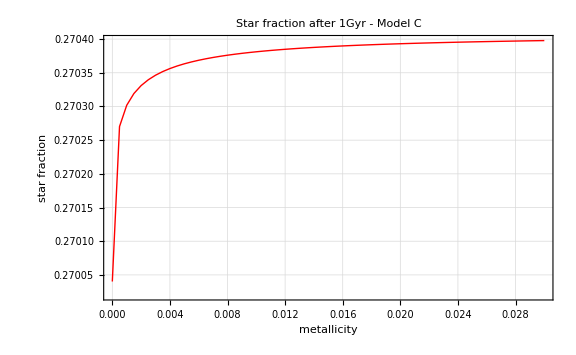

```mathematica
ListPlot[result,
Joined->True,
PlotStyle->{Thick,Red},
FrameLabel->{Style["metallicity",18],Style["star fraction",18] },
FrameStyle->Directive[Black,15],
ImageSize->Large,
Frame->True,
PlotRange->All,
GridLines->Automatic,
PlotLabel->Style["Star fraction after 1Gyr - Model C",20,Bold,Black]]
```